--- At point {0.,0.002} ---

E: {1.16388×10^-7,0.827911,0.}

B: {1.45604×10^-11,7.20325×10^-10,0.}

Shell rho, pr, pt: {3.93669×10^-6,-0.000133737,0.000136099}

BI EC: <|rho→0.78298,p1→0.78298,p2→0.78298,p3→-0.439141,NEC→True,WEC→True,SEC→True,DEC→True|>

Shell EC: <|rho→3.93669×10^-6,p1→0.000136099,p2→0.000136099,p3→-0.000133737,NEC→False,WEC→False,SEC→False,DEC→False|>

Total EC: <|rho→0.782984,p1→0.783116,p2→0.782846,p3→-0.439005,NEC→True,WEC→True,SEC→True,DEC→False|>

Plot: BI energy density u_BI(x,y)

Plot: shell anisotropy Δp = p_t - p_r

Plot: E^2 field intensity

Sample Poynting vectors S(y) along x = 0:

{{-0.04,{0.,0.,1.31047×10^-11}},{-0.035,{0.,0.,3.19406×10^-11}},{-0.03,{0.,0.,6.93916×10^-11}},{-0.025,{0.,0.,1.3406×10^-10}},{-0.02,{0.,0.,2.28765×10^-10}},{-0.015,{0.,0.,3.38465×10^-10}},{-0.01,{0.,0.,4.12378×10^-10}},{-0.005,{0.,0.,3.53788×10^-10}},{0.,{0.,0.,1.02628×10^-10}},{0.005,{0.,0.,-1.79819×10^-10}},{0.01,{0.,0.,-3.07091×10^-10}},{0.015,{0.,0.,-2.9359×10^-10}},{0.02,{0.,0.,-2.18166×10^-10}},{0.025,{0.,0.,-1.36823×10^-10}},{0.03,{0.,0.,-7.46112×10^-11}},{0.035,{0.,0.,-3.58245×10^-11}},{0.04,{0.,0.,-1.52351×10^-11}}}

Radial profiles (shell): rho_s(r), p_r^s(r), p_t^s(r)

Plot: shell rho_s(r)

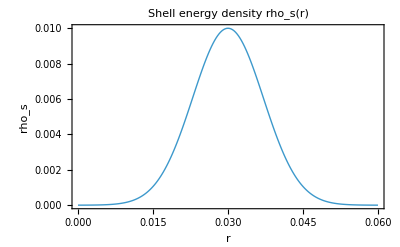

Plot: shell p_r^s(r)

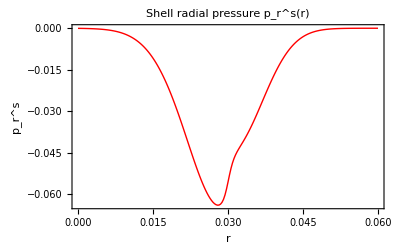

Plot: shell p_t^s(r)

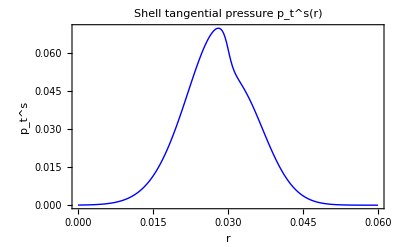

Plot: Shell NEC_s(r) (1 = satisfied, 0 = violated)

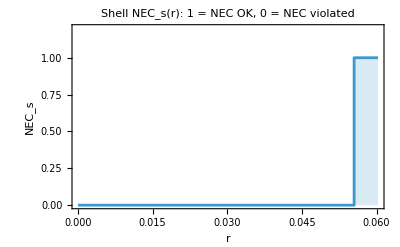

Radial profiles (total): rho_tot(r), p_r^tot(r), p_t^tot(r)

Plot: total rho_tot(r)

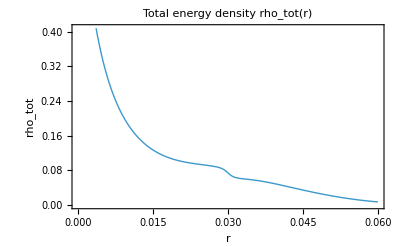

Plot: total p_r^tot(r)

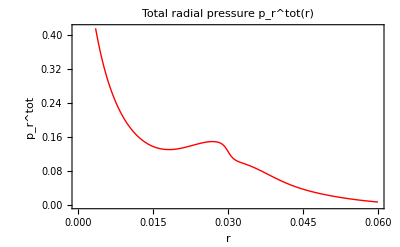

Plot: total p_t^tot(r)

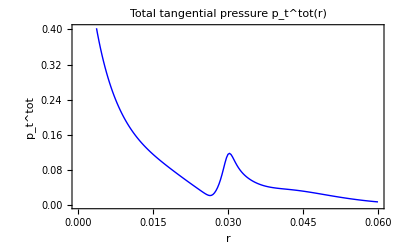

Plot: NEC_tot(r) (1 = satisfied, 0 = violated)

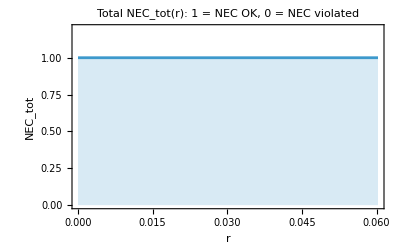

```mathematica
(* =====================================================*)(*PARAMETERS*)(* =====================================================*)ClearAll["Global`*"];

d=0.06;
R0=0.03;
omega=2 Pi 5.0;

bBI=1.0;

bestPars={1.97001,0.685107,4.05734,0.98985,0.753244,0.00139359,-0.902839,3.60618*10^-9};

{A1,A2,phi,m1,m2,epsY,chir1,chir2}=bestPars;

rho0=10*10^-3;
betaR0=0.3;
betaT0=0.3;
gammaR=-50.0;   (*much stronger radial tension from E^2*)
gammaT=50.0;    (*much stronger tangential pressure from E^2*)
wShell=0.01;

t0=0.0;

(* =====================================================*)
(*NUMERIC-SAFE HELPERS*)
(* =====================================================*)

rPlane[x_?NumericQ,y_?NumericQ]:=Sqrt[x^2+y^2];

(* =====================================================*)
(*VORTEX FIELDS*)
(* =====================================================*)

eOneNum[x_?NumericQ,y_?NumericQ,t_?NumericQ,cx_?NumericQ,cy_?NumericQ,A_?NumericQ,phase_?NumericQ,mix_?NumericQ]:=Module[{rx=x-cx,ry=y-cy,rr,g,er,et},rr=Sqrt[rx^2+ry^2];
If[rr<10^-12,{0.,0.,0.},g=Exp[-(rx^2+ry^2)/R0^2];
er={rx/rr,ry/rr,0.};
et={-ry/rr,rx/rr,0.};
A*g*Cos[omega*t+phase]*((1-mix)*er+mix*et)]];

bOneNum[x_?NumericQ,y_?NumericQ,t_?NumericQ,cx_?NumericQ,cy_?NumericQ,A_?NumericQ,phase_?NumericQ,chir_?NumericQ]:=Module[{rx=x-cx,ry=y-cy,rr,g,et},rr=Sqrt[rx^2+ry^2];
If[rr<10^-12,{0.,0.,0.},g=Exp[-(rx^2+ry^2)/R0^2];
et={-ry/rr,rx/rr,0.};
A*g*Sin[omega*t+phase]*chir*et]];

eFieldNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{c1={-d/2,0},c2={d/2,epsY},e1,e2},e1=eOneNum[x,y,t,c1[[1]],c1[[2]],A1,0.,m1];
e2=eOneNum[x,y,t,c2[[1]],c2[[2]],A2,phi,m2];
e1+e2];

bFieldNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{c1={-d/2,0},c2={d/2,epsY},b1,b2},b1=bOneNum[x,y,t,c1[[1]],c1[[2]],A1,0.,chir1];
b2=bOneNum[x,y,t,c2[[1]],c2[[2]],A2,phi,chir2];
b1+b2];

(* =====================================================*)
(*BORN-INFELD INVARIANTS*)
(* =====================================================*)

FInvNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{E=eFieldNum[x,y,t],B=bFieldNum[x,y,t]},0.5*((B.B)-(E.E))];

SNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=1+(2*FInvNum[x,y,t])/bBI^2;

LFNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=-1/Sqrt[SNum[x,y,t]];

DFieldNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{E=eFieldNum[x,y,t],lf=LFNum[x,y,t]},-lf*E];

HFieldNum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{B=bFieldNum[x,y,t],lf=LFNum[x,y,t]},-lf*B];

(* =====================================================*)
(*STRESS-ENERGY TENSOR (Born–Infeld)*)
(* =====================================================*)

stressEnergyBINum[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{E=eFieldNum[x,y,t],B=bFieldNum[x,y,t],D,H,L,u,Sflow,Tij},D=DFieldNum[x,y,t];
H=HFieldNum[x,y,t];
L=bBI^2 (1-Sqrt[SNum[x,y,t]]);
u=E.D-L;
Sflow=Cross[E,H];
Tij=ConstantArray[0.,{4,4}];
Tij[[1,1]]=u;
Tij[[1,2;;4]]=Sflow;
Tij[[2;;4,1]]=Sflow;
Do[Do[Tij[[i+1,j+1]]=-E[[i]]*D[[j]]-B[[i]]*H[[j]]+If[i==j,E.D+B.H-L,0],{j,1,3}],{i,1,3}];
Tij];

(* =====================================================*)
(*ANISOTROPIC SHELL*)
(* =====================================================*)

shellProfile[r_]:=Exp[-(r-R0)^2/wShell^2];

rhoShell[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=rho0*shellProfile[rPlane[x,y]];

E2Num[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{E=eFieldNum[x,y,t]},E.E];

betaR[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=betaR0+gammaR*E2Num[x,y,t];

betaT[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=betaT0+gammaT*E2Num[x,y,t];

pRShell[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=betaR[x,y,t]*rhoShell[x,y,t];

pTShell[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=betaT[x,y,t]*rhoShell[x,y,t];

shellStressTensor[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=Module[{rho=rhoShell[x,y,t],pr=pRShell[x,y,t],pt=pTShell[x,y,t]},{{rho,0,0,0},{0,pr,0,0},{0,0,pt,0},{0,0,0,pt}}];

(* =====================================================*)
(*ENERGY CONDITIONS HELPER*)
(* =====================================================*)

energyConditionsTensor[T_]:=Module[{rho,spatial,evals},rho=T[[1,1]];
spatial=(T[[2;;4,2;;4]]+Transpose[T[[2;;4,2;;4]]])/2;
evals=Eigenvalues[spatial];
<|"rho"->rho,"p1"->evals[[1]],"p2"->evals[[2]],"p3"->evals[[3]],"NEC"->And@@(rho+#>=0&/@evals),"WEC"->(rho>=0&&And@@(rho+#>=0&/@evals)),"SEC"->(And@@(rho+#>=0&/@evals)&&rho+Total[evals]>=0),"DEC"->(rho>=0&&And@@(rho>=Abs[#]&/@evals))|>];

shellEC[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=energyConditionsTensor[shellStressTensor[x,y,t]];

biEC[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=energyConditionsTensor[stressEnergyBINum[x,y,t]];

totalEC[x_?NumericQ,y_?NumericQ,t_?NumericQ]:=energyConditionsTensor[stressEnergyBINum[x,y,t]+shellStressTensor[x,y,t]];

(* =====================================================*)
(*SAMPLE OUTPUT*)
(* =====================================================*)

pt={0.,0.002,t0};

Print["--- At point ",pt[[{1,2}]]," ---"];
Print["E: ",eFieldNum@@pt];
Print["B: ",bFieldNum@@pt];
Print["Shell rho, pr, pt: ",{rhoShell@@pt,pRShell@@pt,pTShell@@pt}];
Print["BI EC: ",biEC@@pt];
Print["Shell EC: ",shellEC@@pt];
Print["Total EC: ",totalEC@@pt];

(* ================================================*)
(*DIAGNOSTIC FIELDS AT t=t0*)
(* ================================================*)

uBI[x_?NumericQ,y_?NumericQ]:=stressEnergyBINum[x,y,t0][[1,1]];
uShell[x_?NumericQ,y_?NumericQ]:=rhoShell[x,y,t0];
uTot[x_?NumericQ,y_?NumericQ]:=uBI[x,y]+uShell[x,y];

deltaPShell[x_?NumericQ,y_?NumericQ]:=pTShell[x,y,t0]-pRShell[x,y,t0];

E2[x_?NumericQ,y_?NumericQ]:=E2Num[x,y,t0];

(* ================================================*)
(*PLOTS*)
(* ================================================*)

range=0.04;   (*adjust if you want bigger view*)

Print["Plot: BI energy density u_BI(x,y)"];
biEnergyPlot=DensityPlot[uBI[x,y],{x,-range,range},{y,-range,range},PlotPoints->40,ColorFunction->"ThermometerColors",FrameLabel->{"x","y"},PlotLabel->"Born-Infeld energy density u_BI"];

Print["Plot: shell anisotropy Δp = p_t - p_r"];
shellAnisoPlot=DensityPlot[deltaPShell[x,y],{x,-range,range},{y,-range,range},PlotPoints->40,ColorFunction->"SolarColors",FrameLabel->{"x","y"},PlotLabel->"Shell anisotropy Δp = p_t - p_r"];

Print["Plot: E^2 field intensity"];
e2Plot=DensityPlot[E2[x,y],{x,-range,range},{y,-range,range},PlotPoints->40,ColorFunction->"AvocadoColors",FrameLabel->{"x","y"},PlotLabel->"E^2(x,y) of vortex"];

(* ================================================*)
(*POYNTING VECTOR SAMPLING ALONG A LINE*)
(* ================================================*)

samplePoynting=Table[Module[{x=0.,yy=y,E=eFieldNum[0.,y,t0],H=HFieldNum[0.,y,t0],S},S=Cross[E,H];
{yy,S}],{y,-range,range,range/8.}];

Print["Sample Poynting vectors S(y) along x = 0:"];
samplePoynting

(* =====================================================*)
(*RADIAL SCAN OF SHELL+TOTAL PROPERTIES*)
(* =====================================================*)

rMin=0.0;
rMax=0.06;
pts=200;

radialData=Table[Module[{x=r,y=0,Tshell,Ttot,rhoS,prS,ptS,necS,rhoT,prT,ptT,necT,spatT,vals},Tshell=shellStressTensor[x,y,t0];
Ttot=stressEnergyBINum[x,y,t0]+Tshell;
rhoS=Tshell[[1,1]];
prS=Tshell[[2,2]];
ptS=Tshell[[3,3]];(*same as[[4,4]]*)rhoT=Ttot[[1,1]];
(*diagonalize spatial part to get principal pressures for total*)spatT=(Ttot[[2;;4,2;;4]]+Transpose[Ttot[[2;;4,2;;4]]])/2;
vals=Eigenvalues[spatT];
prT=vals[[1]];
ptT=vals[[2]];
necS=If[(rhoS+prS>=0)&&(rhoS+ptS>=0),1,0];
necT=If[(rhoT+prT>=0)&&(rhoT+ptT>=0),1,0];
{r,rhoS,prS,ptS,necS,rhoT,prT,ptT,necT}],{r,rMin,rMax,(rMax-rMin)/pts}];

radialR=radialData[[All,1]];
rhoShellR=radialData[[All,2]];
prShellR=radialData[[All,3]];
ptShellR=radialData[[All,4]];
necShellR=radialData[[All,5]];
rhoTotR=radialData[[All,6]];
prTotR=radialData[[All,7]];
ptTotR=radialData[[All,8]];
necTotR=radialData[[All,9]];

(* =====================================================*)
(*PLOTS:SHELL ONLY*)
(* =====================================================*)

Print["Radial profiles (shell): rho_s(r), p_r^s(r), p_t^s(r)"];

rhoShellPlot=ListLinePlot[Transpose[{radialR,rhoShellR}],PlotStyle->Thick,Frame->True,FrameLabel->{"r","rho_s"},PlotLabel->"Shell energy density rho_s(r)"];

prShellPlot=ListLinePlot[Transpose[{radialR,prShellR}],PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"r","p_r^s"},PlotLabel->"Shell radial pressure p_r^s(r)"];

ptShellPlot=ListLinePlot[Transpose[{radialR,ptShellR}],PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{"r","p_t^s"},PlotLabel->"Shell tangential pressure p_t^s(r)"];

Print["Plot: shell rho_s(r)"];rhoShellPlot
Print["Plot: shell p_r^s(r)"];prShellPlot
Print["Plot: shell p_t^s(r)"];ptShellPlot

Print["Plot: Shell NEC_s(r) (1 = satisfied, 0 = violated)"];

necShellPlot=ListStepPlot[Transpose[{radialR,necShellR}],Frame->True,FrameLabel->{"r","NEC_s"},PlotRange->{0,1.2},PlotLabel->"Shell NEC_s(r): 1 = NEC OK, 0 = NEC violated",Filling->Axis];

necShellPlot

(* =====================================================*)
(*PLOTS:TOTAL (BI+SHELL)*)
(* =====================================================*)

Print["Radial profiles (total): rho_tot(r), p_r^tot(r), p_t^tot(r)"];

rhoTotPlot=ListLinePlot[Transpose[{radialR,rhoTotR}],PlotStyle->Thick,Frame->True,FrameLabel->{"r","rho_tot"},PlotLabel->"Total energy density rho_tot(r)"];

prTotPlot=ListLinePlot[Transpose[{radialR,prTotR}],PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"r","p_r^tot"},PlotLabel->"Total radial pressure p_r^tot(r)"];

ptTotPlot=ListLinePlot[Transpose[{radialR,ptTotR}],PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{"r","p_t^tot"},PlotLabel->"Total tangential pressure p_t^tot(r)"];

Print["Plot: total rho_tot(r)"];rhoTotPlot
Print["Plot: total p_r^tot(r)"];prTotPlot
Print["Plot: total p_t^tot(r)"];ptTotPlot

Print["Plot: NEC_tot(r) (1 = satisfied, 0 = violated)"];

necTotPlot=ListStepPlot[Transpose[{radialR,necTotR}],Frame->True,FrameLabel->{"r","NEC_tot"},PlotRange->{0,1.2},PlotLabel->"Total NEC_tot(r): 1 = NEC OK, 0 = NEC violated",Filling->Axis];

necTotPlot
```